## HMQC covariance processing

```mathematica
SetDirectory[NotebookDirectory[] <> "/.."]
```

/Users/mu3q/GitHub/NMRprocess2

```mathematica
Needs["NMRProcess2`"]
```

## Load data

```mathematica
rawfid= ReadBruker["ExampleData/10/ser"]
```

-|Fid..1--

Only the raw NMR acquisition data is loaded, without any information about dwell time, etc. The time domain structure must be set explicitly:

```mathematica
hmqcfid=SetTimeDomain[rawfid,{4096,256}]
```

-|Fid..2--

In order to obtain calibrated plots, we need to set the spectral width (in ppm) and the offsets:

```mathematica
hmqcfid=SetProp[hmqcfid,Offset,{-0.8,96.6}];
hmqcfid=SetProp[hmqcfid,SpectralWidth,{20,90}];
```

## Covariance Transform

```mathematica
covspect = Covariance2D[hmqcfid,Phase2->-2.25,SI2->1024]
```

-|Fid..2--

```mathematica
spect=StatesFFT2[hmqcfid,Phase2->-2.25,Phase1->-0.5,SI1->1024,SI2->4096]
```

-|Fid..2--

## Plots

A full 2D spectrum can be plotted with NMRContourPlot.

The contour levels are automatically set to 10%, 20%, ... of the highest point in the spectrum.
In the present case, we are only interested in a subregion of the spectrum. Crop[]  can be used to reduce the
data:

```mathematica
overview=Crop[spect,{{6.,2.},{120.,60.}}]
```

-|Fid..2--

```mathematica
covoverview=Crop[covspect,{{6.,2.},{120.,60.}}]
```

-|Fid..2--

```mathematica
NMRContourPlot[covspect,Gain->100]
```

-Graphics-

```mathematica
NMRContourPlot[spect,ContourStyle->Red,Gain->1]
```

-Graphics-

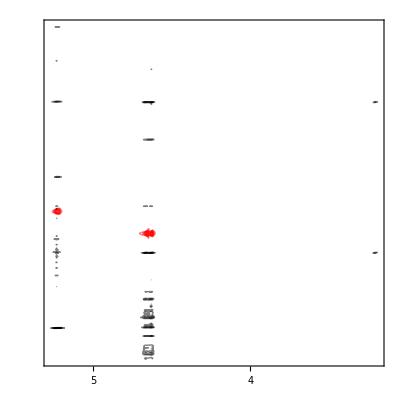

```mathematica
Show[%,%%]
```

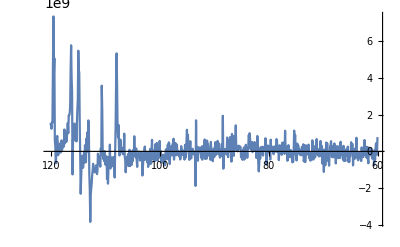

```mathematica
PlotNMR1D[Project[covoverview,{2}],PlotRange->All]
```